# -Graphics-

# Wolfram 语言编程：概念到应用

## 实体和数据集

-Graphics-

## 学习目标

### 实体

基本实体框架

查询实体数据

### 数据集

创建 Dataset

数据集上的各种查询操作

# 实体

## 实体框架

Wolfram 语言™包含可通过实体框架访问的大量现实世界数据，例如：

```mathematica
EntityValue[Entity["Planet","Earth"],EntityProperty["Planet","Diameter"]] (* 地球直径 *)
```

7917.523 mi

```mathematica
EntityValue[Entity["Country","China"],EntityProperty["Country","Population"]] (* 中国人口 *)
```

1433783692 people

```mathematica
EntityValue[Entity["Chemical","Benzene"],EntityProperty["Chemical","ColorStructureDiagram"]] (* 苯的分子结构 *)
```

-Graphics-

获取数据的工作流程：

-Graphics-

使用 Entity 创建实体.

使用 EntityProperty 创建属性.

使用 EntityValue 获取实体的属性值.

地球的直径：

```mathematica
Entity["Planet","Earth"]  (* Entity[<实体类型>, <实体名称>] *)
```

Earth

```mathematica
Entity["Planet","Nonsense"]
```

Entity[Planet,Nonsense]

```mathematica
EntityProperty["Planet","Diameter"] (* EntityProperty[<实体类型>, <属性名称>] *)
```

average diameter

```mathematica
EntityValue[Entity["Planet","Earth"],EntityProperty["Planet","Diameter"]]
```

7917.523 mi

```mathematica
EntityValue[Entity["Planet","Earth"],EntityProperty["Planet","Diameter"]] (* EntityValue[<实体>, <属性>] *)
```

中国人口：

```mathematica
Entity["Country","China"]
```

China

```mathematica
EntityProperty["Country","Population"]
```

population

```mathematica
EntityValue[Entity["Country","China"],EntityProperty["Country","Population"]]
```

1433783692 people

苯分子结构：

```mathematica
Entity["Chemical","Benzene"]
```

benzene

```mathematica
EntityProperty["Chemical","ColorStructureDiagram"]
```

structure diagram

```mathematica
EntityValue[Entity["Chemical","Benzene"],EntityProperty["Chemical","ColorStructureDiagram"]]
```

-Graphics-

## 查找实体和属性

#### 实体类型

Wolfram 语言包含 许多领域的实体类型，例如：

地理实体：国家、城市、海洋、岛屿等

天文实体： 行星、银河、恒星、超新星、 ...

天气和地球科学： TropicalStorm、地震、矿物、...

文化和娱乐： 语言、宗教、电影、音乐作品、...

可以使用 EntityList 查看属于一个实体类型的所有实体的列表：

```mathematica
EntityList["Ocean"]//Shallow
```

{Adriatic Sea,Aegean Sea,Akashi Strait,Alboran Sea,Almyros Bay,Amundsen Gulf,Amundsen Sea,Amurskiy Liman,Anadyrskiy Gulf,Anadyrsky Liman,«237»}

```mathematica
EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
EntityList["Mineral"]//Shallow
```

{abelsonite,abernathyite,abhurite,abswurmbachite,acetamide,achavalite,actinolite,acuminite,adamite,adamsite-(Y),«3868»}

```mathematica
EntityList["Movie"]//Shallow
```

{-30-,00 Schneider – Jagd auf Nihil Baxter,06/05,08/15 Part 2,0:0 (Teko Efes),Ten Thousand Saints,10,000 BC,Different Kinds of Rain,1,000 Dollars a Minute,1 0 0 (Alexandras 173, Athina),«54331»}

#### 实体属性

可以使用 EntityProperties 查看与实体类型关联的所有属性：

```mathematica
EntityProperties["Ocean"]//Shallow
```

{ACICM491 code,area,average depth,basins,bordering bodies of water,bordering continents,bordering countries,center coordinates,coastline length,countries,«24»}

```mathematica
EntityProperties["Planet"]//Shallow
```

{absolute magnitude H,age,albedo,alphanumeric name,altitude,next maximum altitude,angular diameter,angular radius,largest distance from the Sun,largest distance from Sun,«122»}

```mathematica
EntityProperties["Mineral"]//Shallow
```

{2V angle,alternate names,birefringence,cleavage,color,crystal system,Dana ID,density,transparency,discovery year,«26»}

```mathematica
EntityProperties["Movie"]//Shallow
```

{rating advisory,cast,cast and roles,company,director,US box office total receipts,US daily box office change in receipts,US daily box office receipts,US daily box office rank,total daily US box office receipts,«32»}

调用检索实体属性值的方法：

```mathematica
EntityValue[Entity["Ocean","AdriaticSea"],EntityProperty["Ocean","AverageDepth"]]
```

-1457. ft

```mathematica
EntityValue[Entity["Planet","Earth"],EntityProperty["Planet","Apoapsis"]]
```

9.450913×10^7 mi

## 查找实体和属性

#### 自动补全

在填充 Entity 或 EntityProperty 参数时，Wolfram 语言显示可用实体类型和属性的列表：

```mathematica
EntityProperty["Country","Population"]
```

-Graphics-
-Graphics-
-Graphics-

#### 通过自然语言查找实体

使用   构建实体：

```mathematica
LinguisticAssistant
```

请注意，有时可能难以使用通常的语法来创建：

```mathematica
Entity["City","Paris"]
```

Entity[City,Paris]

```mathematica
Entity["City",{"Paris","IleDeFrance","France"}]//FullForm
```

Entity["City",List["Paris","IleDeFrance","France"]]

```mathematica
Entity["City",{"Paris","IleDeFrance","France"}]
```

Paris

```mathematica
Entity["City",{"Paris","IleDeFrance","France"}]
```

Paris

```mathematica
Entity["Airline","AmericanAirlinesInc::24y82"]
```

```mathematica
Entity["Airline","AmericanAirlines"]
```

Entity[Airline,AmericanAirlines]

```mathematica
Entity["Airline","AmericanAirlinesInc::24y82"]//FullForm
```

Entity["Airline","AmericanAirlinesInc::24y82"]

```mathematica
LinguisticAssistant
```

American Airlines Inc.

```mathematica
Entity["Airline","AmericanAirlinesInc::24y82"]
```

## 有关语法的更多信息

#### 其他语法

您已学习的语法：

```mathematica
EntityValue[Entity["Planet","Earth"],EntityProperty["Planet","Diameter"]]
```

7917.523 mi

可以使用<实体> [<实体属性>]或<实体属性> [<实体>]：

```mathematica
Entity["Planet","Earth"][EntityProperty["Planet","Diameter"]]
```

7917.523 mi

```mathematica
EntityProperty["Planet","Diameter"][Entity["Planet","Earth"]]
```

7917.523 mi

规范名称可用于实体属性：

```mathematica
CanonicalName[EntityProperty["Planet","Diameter"]]
```

Diameter

```mathematica
EntityValue[Entity["Planet","Earth"],"Diameter"]
```

7917.523 mi

#### 多个查询

可以同时进行多个查询：

```mathematica
EntityValue[Entity["Planet","Earth"],{EntityProperty["Planet","Diameter"],EntityProperty["Planet","Apoapsis"],EntityProperty["Planet","Density"]}]
```

{7917.523 mi,9.450913×10^7 mi,5.515 g/cm^3}

```mathematica
EntityValue[{Entity["Planet","Earth"],Entity["Planet","Mars"],Entity["Planet","Jupiter"]},EntityProperty["Planet","Diameter"]]
```

{7917.523 mi,4212. mi,86920. mi}

```mathematica
EntityValue[{Entity["Planet","Earth"],Entity["Planet","Mars"],Entity["Planet","Jupiter"]},{EntityProperty["Planet","Diameter"],EntityProperty["Planet","Apoapsis"],EntityProperty["Planet","Density"]}]
```

{{7917.523 mi,9.450913×10^7 mi,5.515 g/cm^3},{4212. mi,1.5486355×10^8 mi,3.934 g/cm^3},{86920. mi,5.0708951×10^8 mi,1.3262 g/cm^3}}

## EntityPrefetch

EntityPrefetch 可用于将实体数据下载到本地计算机，以加快检索速度：

```mathematica
AbsoluteTiming[EntityValue[Entity["Volcano","Baekdu"],EntityProperty["Volcano","Elevation"]]]
```

{1.81383,9002.62 ft}

```mathematica
AbsoluteTiming[EntityValue[Entity["Volcano","Kos"],{EntityProperty["Volcano","Countries"],EntityProperty["Volcano","Latitude"],EntityProperty["Volcano","Longitude"]}]]
```

{3.71262,{{Greece},36.852 °,27.251 °}}

```mathematica
AbsoluteTiming[EntityValue[Entity["Volcano","Saba"],EntityProperty["Volcano","Image"]]]
```

{1.40304,-Graphics-}

```mathematica
FileNameJoin[{$UserBaseDirectory,"Knowledgebase"}]//SystemOpen (* 缓存数据存在此 *)
```

```mathematica
EntityPrefetch["Volcano"]
```

Success[…]

下载后：

```mathematica
AbsoluteTiming[EntityValue[Entity["Volcano","Baekdu"],EntityProperty["Volcano","Elevation"]]]
```

{0.002727,9002.62 ft}

```mathematica
AbsoluteTiming[EntityValue[Entity["Volcano","Kos"],{EntityProperty["Volcano","Countries"],EntityProperty["Volcano","Latitude"],EntityProperty["Volcano","Longitude"]}]]
```

{0.00817,{{Greece},36.852 °,27.251 °}}

```mathematica
AbsoluteTiming[EntityValue[Entity["Volcano","Saba"],EntityProperty["Volcano","Image"]]]
```

{0.001241,-Graphics-}

# Dataset

## Dataset

在 Wolfram 语言中，数据集表示可以在其上执行查询的数据的结构化表示.

#### 动物的重量

```mathematica
e1= ResourceData["Sample Data: Animal Weights"]
```

```mathematica
e1[1;;10,{"Species","BodyWeight"}] (* 查看前 10 个的体重 *)
```

#### 行星数据

```mathematica
e2=ExampleData[{"Dataset","Planets"}]
```

```mathematica
e2[All,"Radius"] (* 行星的半径 *)
```

```mathematica
e2[All,"Moons",Values/*<|"Average Moon Radius"->Mean|>,"Radius"] (* 平均卫星半径 *)
```

#### 泰坦尼克号乘客

```mathematica
e3=ExampleData[{"Dataset","Titanic"}]
```

```mathematica
e3[Counts,"class"] (* 每级舱位的乘客数 *)
```

```mathematica
e3[Counts,"sex"] (* 性别数量 *)
```

## 创建数据集

数据集函数可以应用于包含列表和关联的表达式，以创建数据集实例.

#### 没有标头

```mathematica
list2d={{1,2,3},{4,5,6},{7,8,9}};
MatrixForm[list2d]
Dataset[list2d]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

#### 带列标头

关联列表——每个关联代表一条记录：

```mathematica
Dataset[{<|"c1"->1,"c2"->2,"c3"->3|>,
	       <|"c1"->4,"c2"->5,"c3"->6|>,
	       <|"c1"->7,"c2"->8,"c3"->9|>}]
```

请注意，您不能使用外部关联——重复项将被删除：

```mathematica
<|<|"c1"->1,"c2"->2,"c3"->3|>,<|"c1"->2,"c2"->4,"c3"->6|>,<|"c1"->3,"c2"->6,"c3"->9|>|>
```

<|c1→3,c2→6,c3→9|>

#### 带行和列标头

记录使用规则命名. 使用外部关联而不是外部列表.

```mathematica
Dataset[<|"r1"-><|"c1"->1,"c2"->2,"c3"->3|>,
                "r2"-><|"c1"->4,"c2"->5,"c3"->6|>,
                "r3"-><|"c1"->7,"c2"->8,"c3"->9|>|>]
```

#### 可以进行任意深度嵌套（可选）

```mathematica
pl=Dataset[<|"Earth"-><|"Mass"->Quantity[5.9721986*10^24,"Kilograms"],
					"Radius"->Quantity[6367.4447,"Kilometers"],
					"Moons"-><|"Moon"-><|"Mass"->Quantity[7.3459*10^22,"Kilograms"],"Radius"->Quantity[1737.5,"Kilometers"]|>|>|>,
			 "Mars"-><|"Mass"->Quantity[6.41693*10^23,"Kilograms"],
					"Radius"->Quantity[3386.,"Kilometers"],
					"Moons"-><|"Phobos"-><|"Mass"->Quantity[1.072*10^16,"Kilograms"],"Radius"->Quantity[11.1,"Kilometers"]|>,
							    "Deimos"-><|"Mass"->Quantity[1.5*10^15,"Kilograms"],"Radius"->Quantity[6.2,"Kilometers"]|>|>|>|>]
```

## 从数据集中选择元素

从数据集中选择元素与从矩阵选择元素非常相似.

使用 k1、k2、k3 提醒自己，这些是关联中的键：

```mathematica
mat={{1,2,3},{4,5,6},{7,8,9}};
MatrixForm[mat]
ds=Dataset[{<|"k1"->1,"k2"->2,"k3"->3|>,<|"k1"->4,"k2"->5,"k3"->6|>,<|"k1"->7,"k2"->8,"k3"->9|>}]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

#### 选择行

矩阵：

```mathematica
mat[[1]]
```

{1,2,3}

```mathematica
mat[[2;;3]]
```

{{4,5,6},{7,8,9}}

数据集——您需要一对方括号：

```mathematica
ds[1;;2]
```

```mathematica
ds[2;;3]
```

#### 选择列

```mathematica
mat//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
ds
```

```mathematica
mat[[All,1]]
```

{1,4,7}

```mathematica
mat[[All,3]]
```

{3,6,9}

```mathematica
ds[All,1] (* 列数 *)
```

```mathematica
ds[All,"k1"] (* 列名 *)
```

```mathematica
ds[All,3]
```

```mathematica
ds[All,"k3"]
```

#### 选择元素

```mathematica
mat//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
ds
```

```mathematica
mat[[1,2]]
```

2

```mathematica
mat[[2,3]]
```

6

```mathematica
ds[1,2]
```

2

```mathematica
ds[1,"k1"]
```

1

```mathematica
ds[2,3]
```

6

```mathematica
ds[2,"k3"]
```

6

#### 嵌套数据集（可选）

```mathematica
pl
```

```mathematica
pl["Earth"]
```

```mathematica
pl[All,"Mass"]
```

```mathematica
pl["Mars","Moons"]
```

```mathematica
pl["Mars","Moons",Keys]
```

```mathematica
pl["Mars","Moons","Phobos"]
```

```mathematica
pl["Mars","Moons","Phobos","Mass"]
```

1.072×10^16 kg

```mathematica
pl["Mars","Moons",All,"Mass"]
```

```mathematica
pl[All,"Moons",All,"Mass"]
```

## 查询数据集

#### 等级

数据集上的运算符的行为类似于从嵌套列表中选择元素：

```mathematica
nestedList={{x,y},{ 0, 5},{Red,{Green,Blue}}}
```

{{x,y},{0,5},{RGBColor[1, 0, 0],{RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}}

```mathematica
nestedList[[3]]
```

{RGBColor[1, 0, 0],{RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

```mathematica
nestedList[[3,1]]
```

RGBColor[1, 0, 0]

```mathematica
nestedList[[3,2,2]]
```

RGBColor[0, 0, 1]

在数据集上：

```mathematica
ds
```

```mathematica
dsNormal=Normal[ds]
```

{<|k1→1,k2→2,k3→3|>,<|k1→4,k2→5,k3→6|>,<|k1→7,k2→8,k3→9|>}

```mathematica
ds[f1]
```

f1[{<|k1→1,k2→2,k3→3|>,<|k1→4,k2→5,k3→6|>,<|k1→7,k2→8,k3→9|>}]

```mathematica
ds[f1,f2]
```

f1[{f2[<|k1→1,k2→2,k3→3|>],f2[<|k1→4,k2→5,k3→6|>],f2[<|k1→7,k2→8,k3→9|>]}]

```mathematica
ds[f1,f2,f3]
```

f1[{f2[<|k1→f3[1],k2→f3[2],k3→f3[3]|>],f2[<|k1→f3[4],k2→f3[5],k3→f3[6]|>],f2[<|k1→f3[7],k2→f3[8],k3→f3[9]|>]}]

#### 顺序

数据集中的有效运算符可以分为两类：

降序运算符（或过滤运算符）：Select、GroupBy、SortBy…

升序运算符（或聚合运算符）：Total、Min、Histogram…

首先从左到右应用降序运算符，朝着数据的最内层应用. 然后，从右到左应用升序运算符，朝最外层进行.

表达式ds[a1, d1, d2, a2, a3, d3, a4]的应用顺序，其中 a_i 和 d_i 分别表示升序和降序运算符：

d1 → d2 → d3 → a4 → a3 → a2 → a1

以下示例显示了三个运算符的应用. 其中级别和顺序的应用将在后面说明：

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
```

```mathematica
titanic[GroupBy["class"],Histogram,"age"]
```

## 查询数据集（续）

#### 运算符格式

数据集查询经常使用函数的运算符形式：

```mathematica
Select[{1,2,3,4,5,6},EvenQ] (* 标准语法 *)
```

{2,4,6}

```mathematica
Select[EvenQ][{1,2,3,4,5,6}] (* 运算符格式 *)
```

{2,4,6}

```mathematica
Cases[{1,2,3,4,5,6},x_/;x>3] (* 标准语法 *)
```

{4,5,6}

```mathematica
Cases[x_/;x>3][{1,2,3,4,5,6}] (* 运算符格式 *)
```

{4,5,6}

#### 结构（回顾）

具有列标头的数据集是关联列表：

```mathematica
ds//Normal
```

{<|k1→1,k2→2,k3→3|>,<|k1→4,k2→5,k3→6|>,<|k1→7,k2→8,k3→9|>}

因此，了解函数如何在关联上工作对于了解数据集查询很有帮助.

#### 关联操作

几个函数直接作用于值：

```mathematica
(#^2+1)&[<|"k1"->3,"k2"->2,"k3"->1|>]
```

<|k1→10,k2→5,k3→2|>

```mathematica
Total[<|"k1"->3,"k2"->2,"k3"->1|>]
```

6

```mathematica
Sort[<|"k1"->3,"k2"->2,"k3"->1|>]
```

<|k3→1,k2→2,k1→3|>

也适用于关联列表：

```mathematica
(#^2+#+1)&[{<|"k1"->3,"k2"->2,"k3"->1|>,<|"k1"->2,"k2"->4,"k3"->6|>,<|"k1"->3,"k2"->6,"k3"->9|>}]
```

{<|k1→13,k2→7,k3→3|>,<|k1→7,k2→21,k3→43|>,<|k1→13,k2→43,k3→91|>}

```mathematica
Total[{<|"k1"->3,"k2"->2,"k3"->1|>,<|"k1"->2,"k2"->4,"k3"->6|>,<|"k1"->3,"k2"->6,"k3"->9|>}]
```

<|k1→8,k2→12,k3→16|>

纯函数可以与键标签一起使用：

```mathematica
#k1&[<|"k1"->2,"k2"->4,"k3"->6|>]
```

2

```mathematica
Select[{<|"k1"->1,"k2"->2|>,<|"k1"->3,"k2"->4|>,<|"k1"->5,"k2"->7|>,<|"k1"->7,"k2"->7|>},#k1>3&]
```

{<|k1→5,k2→7|>,<|k1→7,k2→7|>}

```mathematica
SelectFirst[{<|"k1"->1,"k2"->2|>,<|"k1"->3,"k2"->4|>,<|"k1"->5,"k2"->7|>,<|"k1"->7,"k2"->7|>},#k1>3&]
```

<|k1→5,k2→7|>

## 筛选运算符

过滤运算符通过产生较小的数据集来过滤数据. 后续运算符可应用于以下各项：

```mathematica
ds2=Dataset[{
<|"k1"->1,"k2"->"x","k3"->{1}|>,
<|"k1"->2,"k2"->"y","k3"->{2,3}|>,
<|"k1"->3,"k2"->"z","k3"->{4,5,6}|>,
<|"k1"->4,"k2"->"x","k3"->{7,8,9,10}|>}]
```

#### 例子1

```mathematica
ds2[Select[#k1>2&]]
```

分解：

```mathematica
ds2Normal=Normal[ds2]
```

{<|k1→1,k2→x,k3→{1}|>,<|k1→2,k2→y,k3→{2,3}|>,<|k1→3,k2→z,k3→{4,5,6}|>,<|k1→4,k2→x,k3→{7,8,9,10}|>}

```mathematica
Select[#k1>2&][ds2Normal]
```

{<|k1→3,k2→z,k3→{4,5,6}|>,<|k1→4,k2→x,k3→{7,8,9,10}|>}

```mathematica
Dataset[%]
```

#### 例子2

```mathematica
ds2[All,"k3",Select[EvenQ]]
```

分解：（请注意，所有运算符都是降序的）：

```mathematica
ds2Normal[[All]] (* level 1 *)
```

{<|k1→1,k2→x,k3→{1}|>,<|k1→2,k2→y,k3→{2,3}|>,<|k1→3,k2→z,k3→{4,5,6}|>,<|k1→4,k2→x,k3→{7,8,9,10}|>}

```mathematica
#["k3"]&/@ds2Normal[[All]] (* level 2 *)
```

{{1},{2,3},{4,5,6},{7,8,9,10}}

```mathematica
Select[EvenQ][#]&/@{{1},{2,3},{4,5,6},{7,8,9,10}} (* level 3 *)
```

{{},{2},{4,6},{8,10}}

```mathematica
Dataset[%]
```

#### 更多示例（可选）

```mathematica
ds2[All,KeySelect[StringMatchQ["k1"|"k2"]]]
```

```mathematica
ds2Normal[[All]]
```

{<|k1→1,k2→x,k3→{1}|>,<|k1→2,k2→y,k3→{2,3}|>,<|k1→3,k2→z,k3→{4,5,6}|>,<|k1→4,k2→x,k3→{7,8,9,10}|>}

```mathematica
KeySelect[#,StringMatchQ["k1"|"k2"]]&/@%
```

{<|k1→1,k2→x|>,<|k1→2,k2→y|>,<|k1→3,k2→z|>,<|k1→4,k2→x|>}

```mathematica
Dataset@%
```

```mathematica
ds2[Select[#k1>2&],KeySelect[StringMatchQ["k1"|"k2"]]]
```

```mathematica
Select[#k1>2&]@ds2Normal
```

{<|k1→3,k2→z,k3→{4,5,6}|>,<|k1→4,k2→x,k3→{7,8,9,10}|>}

```mathematica
KeySelect[#,StringMatchQ["k1"|"k2"]]&/@%
```

{<|k1→3,k2→z|>,<|k1→4,k2→x|>}

```mathematica
Dataset@%
```

参考：

-Graphics-

## 变换运算符

```mathematica
ds3=Dataset[<|"r1"-><|"k1"->1,"k2"->2,"k3"->3|>,
		          "r2"-><|"k1"->4,"k2"->5,"k3"->6|>,
			 "r3"-><|"k1"->7,"k2"->8,"k3"->9|>|>]
```

#### 例子1

```mathematica
ds3[#^2&]
```

分解：

```mathematica
ds3Normal=Normal[ds3]
```

<|r1→<|k1→1,k2→2,k3→3|>,r2→<|k1→4,k2→5,k3→6|>,r3→<|k1→7,k2→8,k3→9|>|>

```mathematica
#^2&[ds3Normal]
```

<|r1→<|k1→1,k2→4,k3→9|>,r2→<|k1→16,k2→25,k3→36|>,r3→<|k1→49,k2→64,k3→81|>|>

```mathematica
Dataset[%]
```

## 合并运算符

```mathematica
ds4=Dataset[{
<|"a"->1,"b"->"x","c"->{1}|>,
<|"a"->2,"b"->"y","c"->{2,3}|>,
<|"a"->3,"b"->"z","c"->{4,5,6}|>,
<|"a"->4,"b"->"x","c"->{7,8,9,10}|>}]
```

#### 例子1

```mathematica
ds4[All,"c",Total]
```

```mathematica
ds4Normal=Normal[ds4]
```

{<|a→1,b→x,c→{1}|>,<|a→2,b→y,c→{2,3}|>,<|a→3,b→z,c→{4,5,6}|>,<|a→4,b→x,c→{7,8,9,10}|>}

```mathematica
s1=ds4Normal[[All]]
```

{<|a→1,b→x,c→{1}|>,<|a→2,b→y,c→{2,3}|>,<|a→3,b→z,c→{4,5,6}|>,<|a→4,b→x,c→{7,8,9,10}|>}

```mathematica
s2=#c&/@s1
```

{{1},{2,3},{4,5,6},{7,8,9,10}}

```mathematica
s3=Total/@s2
```

{1,5,15,34}

```mathematica
Dataset[%]
```

#### 例子2

```mathematica
ds4[Mean,"c",Total]
```

55/4

分解：（请注意， Mean 和 Total 是升序运算符；#c&  是降序运算符）：

```mathematica
ds4Normal
```

{<|a→1,b→x,c→{1}|>,<|a→2,b→y,c→{2,3}|>,<|a→3,b→z,c→{4,5,6}|>,<|a→4,b→x,c→{7,8,9,10}|>}

```mathematica
Mean[ds4Normal]
```

Mean::rectt: Mean[{<|a→1,b→x,c→{1}|>,<|a→2,b→y,c→{2,3}|>,<|a→3,b→z,c→{4,5,6}|>,<|a→4,b→x,c→{7,8,9,10}|>}] 中位置 1 处应该是矩形数组.

Mean[{<|a→1,b→x,c→{1}|>,<|a→2,b→y,c→{2,3}|>,<|a→3,b→z,c→{4,5,6}|>,<|a→4,b→x,c→{7,8,9,10}|>}]

```mathematica
s1=#c&/@ds4Normal
```

{{1},{2,3},{4,5,6},{7,8,9,10}}

```mathematica
s2=Total/@s1
```

{1,5,15,34}

```mathematica
s3=Mean@s2
```

55/4

#### 例子3

```mathematica
titanic
```

```mathematica
titanic[GroupBy["class"],Histogram,"age"]
```

分解：

GroupBy [“ class”]和 #age& 是降序，其中 Histogram 是升序：

```mathematica
titanicNormal=Normal[titanic];
```

```mathematica
s1=GroupBy[#class&][titanicNormal]
```

<|1st→{<|class→1st,age→29,sex→female,survived→True|>,<|class→1st,age→1,sex→male,survived→True|>,320,<|class→1st,age→36,sex→female,survived→True|>},2nd→{1},3rd→{1}|>
 |  |  |  |

```mathematica
s2=Map[#age&,s1,{2}]
```

<|1st→{29,1,2,30,25,48,63,39,53,71,47,18,24,26,80,Missing[],24,50,32,36,37,47,26,42,29,25,25,19,35,28,45,40,30,58,42,45,22,Missing[],41,48,Missing[],44,59,60,41,45,Missing[],42,53,36,58,33,28,17,11,14,36,36,49,Missing[],36,76,46,47,27,33,36,30,45,Missing[],Missing[],27,26,22,Missing[],47,39,37,64,55,Missing[],70,36,64,39,38,51,27,33,31,27,31,17,53,4,54,50,27,48,48,49,39,23,38,54,36,Missing[],Missing[],Missing[],36,30,24,28,23,19,64,60,30,Missing[],50,43,Missing[],22,60,48,Missing[],37,35,47,35,22,45,24,49,Missing[],71,53,19,38,58,23,45,46,25,25,48,49,Missing[],45,35,40,27,Missing[],24,55,52,42,Missing[],55,16,44,51,42,35,35,38,Missing[],35,38,50,49,46,50,33,58,41,Missing[],42,45,Missing[],39,49,30,35,Missing[],42,55,16,51,29,21,30,58,15,30,16,Missing[],19,18,24,46,54,36,28,Missing[],65,44,33,37,30,55,47,37,31,23,58,19,64,39,Missing[],22,65,29,Missing[],46,23,29,22,18,17,30,52,47,56,38,Missing[],22,Missing[],43,31,45,Missing[],33,46,36,33,55,54,33,13,18,21,61,48,Missing[],24,Missing[],35,30,34,40,35,50,39,56,28,56,56,24,Missing[],18,24,23,6,45,40,57,Missing[],32,62,54,43,52,Missing[],62,67,63,61,48,18,52,39,48,Missing[],49,17,39,Missing[],31,40,61,47,35,64,60,60,54,21,55,31,57,45,50,27,50,21,51,21,Missing[],31,Missing[],62,36},2nd→{30,28,30,18,25,34,36,57,18,23,36,28,51,32,19,28,1,4,12,36,34,19,23,26,42,27,24,15,60,40,20,25,36,25,42,42,1,26,22,35,Missing[],19,44,54,52,37,29,25,45,29,28,29,28,24,8,31,31,22,30,Missing[],21,Missing[],8,18,48,28,32,17,29,24,25,18,18,34,54,8,42,34,27,30,23,21,18,40,29,18,36,Missing[],38,35,38,34,34,16,26,47,21,21,24,24,34,30,52,30,1,24,44,6,28,62,30,7,43,45,24,24,49,48,55,24,32,21,18,20,23,36,54,50,44,29,21,42,63,60,33,17,42,24,47,24,22,32,23,34,24,22,Missing[],35,45,57,Missing[],31,26,30,Missing[],1,3,25,22,17,Missing[],34,36,24,61,50,42,57,Missing[],1,31,24,Missing[],30,40,32,30,46,13,41,19,39,48,70,27,54,39,16,62,33,14,2,3,37,26,19,28,20,29,39,22,Missing[],23,29,28,Missing[],50,19,Missing[],41,21,19,43,32,34,30,27,2,8,33,36,34,30,28,23,1,3,24,50,19,21,26,25,27,25,18,20,30,59,30,35,40,25,41,25,19,14,50,23,28,27,29,27,40,31,30,23,31,Missing[],12,40,33,27,29,2,4,29,1,5,36,33,66,Missing[],31,Missing[],26,24},3rd→{42,13,16,35,16,25,20,18,30,26,40,1,18,26,26,20,24,25,35,18,32,19,4,6,2,17,38,9,11,39,27,26,39,20,26,25,18,24,35,5,9,3,13,5,40,23,38,45,21,23,17,30,23,13,20,32,33,1,1,5,24,18,40,26,20,18,45,27,22,19,26,22,Missing[],20,32,21,18,26,6,9,Missing[],Missing[],Missing[],40,32,21,22,20,29,22,22,35,19,21,19,18,21,30,18,38,17,17,21,21,21,Missing[],Missing[],28,24,16,37,28,24,21,32,29,26,18,20,18,24,36,24,31,31,22,30,71,43,35,27,19,30,9,3,36,59,19,17,44,17,23,45,22,19,30,29,1,34,28,27,25,24,22,21,17,Missing[],Missing[],37,36,30,16,1,1,26,33,25,Missing[],Missing[],22,36,19,17,42,43,Missing[],32,19,30,24,23,33,65,24,23,22,18,16,45,Missing[],39,17,15,47,5,Missing[],41,41,Missing[],18,Missing[],Missing[],Missing[],26,Missing[],Missing[],21,9,Missing[],18,16,48,Missing[],Missing[],25,Missing[],Missing[],22,16,Missing[],9,33,41,31,38,9,1,11,10,16,14,40,43,51,32,Missing[],20,37,28,19,24,17,Missing[],Missing[],28,24,20,24,41,26,21,45,Missing[],25,Missing[],11,Missing[],27,Missing[],18,26,23,22,28,28,Missing[],2,22,43,28,27,Missing[],Missing[],42,Missing[],30,Missing[],27,25,Missing[],29,21,Missing[],20,48,17,Missing[],Missing[],34,26,22,33,31,29,4,1,49,33,19,27,Missing[],Missing[],Missing[],Missing[],23,32,27,20,21,32,17,21,30,21,33,22,4,39,Missing[],19,Missing[],Missing[],Missing[],Missing[],35,44,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],22,26,4,29,26,1,18,36,Missing[],25,Missing[],37,Missing[],Missing[],Missing[],22,Missing[],26,29,29,22,22,Missing[],Missing[],Missing[],Missing[],Missing[],32,35,Missing[],Missing[],36,39,24,25,45,36,30,20,Missing[],28,Missing[],30,26,Missing[],21,27,51,23,32,Missing[],Missing[],Missing[],24,22,Missing[],Missing[],Missing[],29,Missing[],31,Missing[],Missing[],35,33,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],15,35,Missing[],24,19,Missing[],Missing[],Missing[],56,Missing[],21,Missing[],24,21,28,Missing[],Missing[],25,6,27,Missing[],Missing[],Missing[],Missing[],34,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],24,Missing[],Missing[],Missing[],Missing[],18,22,15,1,20,19,33,Missing[],Missing[],Missing[],Missing[],12,14,29,28,18,26,21,41,39,21,29,22,61,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],23,Missing[],Missing[],Missing[],22,Missing[],Missing[],9,28,42,Missing[],31,28,32,20,23,20,20,16,31,Missing[],2,6,3,8,29,1,7,2,16,14,41,21,19,Missing[],32,1,3,26,Missing[],Missing[],Missing[],21,25,22,25,Missing[],Missing[],Missing[],Missing[],24,28,19,Missing[],25,18,32,Missing[],17,24,Missing[],Missing[],Missing[],Missing[],38,21,10,4,7,2,8,39,22,35,Missing[],Missing[],Missing[],50,47,Missing[],Missing[],2,18,41,Missing[],50,16,Missing[],Missing[],Missing[],25,Missing[],Missing[],Missing[],39,Missing[],15,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],24,21,39,Missing[],Missing[],Missing[],1,24,4,25,20,25,Missing[],Missing[],Missing[],29,Missing[],Missing[],Missing[],Missing[],22,Missing[],40,21,18,4,10,9,2,40,45,Missing[],Missing[],Missing[],Missing[],Missing[],19,30,Missing[],32,Missing[],33,23,21,61,19,22,31,27,2,29,16,44,25,74,14,24,25,34,1,Missing[],Missing[],Missing[],16,Missing[],Missing[],Missing[],32,Missing[],Missing[],31,44,Missing[],25,Missing[],7,9,29,36,18,63,Missing[],12,41,10,36,30,Missing[],33,28,28,47,18,31,16,31,22,20,14,22,22,Missing[],Missing[],Missing[],33,38,51,18,21,47,Missing[],Missing[],Missing[],29,21,27,Missing[],36,27,15,46,Missing[],Missing[],15,Missing[],27,27,29}|>

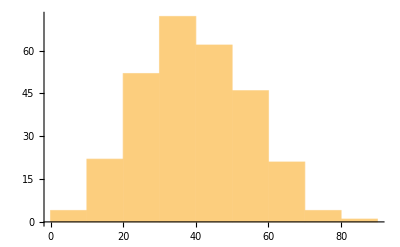
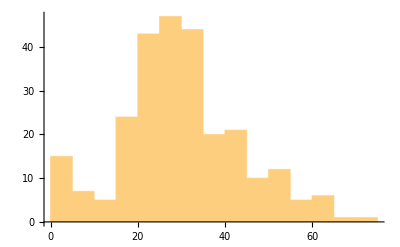
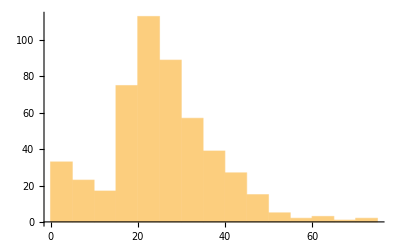
<|1st→-Graphics-,2nd→-Graphics-,3rd→-Graphics-|>

```mathematica
s3=Histogram/@s2
```

```mathematica
Dataset[%]
```

参考：

-Graphics-

## 总结

讨论了基本实体框架和查询实体数据的方法.

EntityPrefetch 可用于将实体数据下载到本地计算机，以加快检索速度.

讨论了创建各种类型的数据集的过程.

为了了解数据集查询，了解关联的操作很重要.

各种数据集操作，例如讨论了过滤、合并、选择.

## Initialization

```mathematica
SetOptions[Plot,PlotStyle->Orange];
```